```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2);Nx=100;max=100;
```

```mathematica
α=0.1;m =5/2;λ=π/2;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[If[EvenQ[Abs[i-n]],NIntegrate[ϕ[i][p]H[n][p],{p,-max,max},MaxRecursion->50],0],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues@Last[%]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in p near {p} = {33.0318}. NIntegrate obtained -39.0919 and 20.9817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in p near {p} = {-32.8217}. NIntegrate obtained 70.5772 and 12.3466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in p near {p} = {32.8828}. NIntegrate obtained 43.5641 and 22.2969 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Eigenvalues@{{5.389519820437078,0.06319507386394632,-1.3910769933774296,-0.10972265356167549,0.4025059496538697,0.017777960681685308},{-0.04348232608472976,8.192069753485976,0.028495156153022283,-3.6321363729804217,0.1085357500151636,-0.019201693172551396},{-1.3744904530913347,-0.02383619329094227,8.104799247111806,0.12675953538316515,-2.841989397914443,-1.1293049828609014*^-13},{0.002866900097604064,-2.883656503260522,0.016557387127103293,11.592826698811564,0.02474506270605197,-0.365782246493661},{-1.0958726998567192,0.018179297463478173,-3.027057883408656,0.13139639646891219,14.412470856564667,0.030269901898252044},{-0.048503012351797006,-0.24779180060171338,-0.01214083302672399,-3.136565876229588,0.15387537609163549,14.212020796422022}}
```

{15.5246,14.8472,12.958,7.77439,6.18573,4.61382}

```mathematica
NIntegrate[ϕ[5][p]H[2][p],{p,-max,max},MaxRecursion->10]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {16.0141}. NIntegrate obtained 4.76841×10^-14 and 2.14574×10^-13 for the integral and error estimates.

4.76841×10^-14

```mathematica
NIntegrate[ϕ[0][p]H[0][p],{p,-max,max},MaxRecursion->100]
```

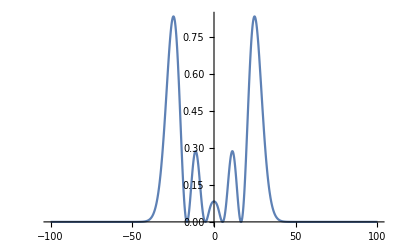

```mathematica
Plot[ϕ[4][p]H[4][p],{p,-100,100},PlotRange->All]
```

```mathematica
NIntegrate[ϕ[0][p]H[0][p],{p,-max,max},MaxRecursion->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.45125 and 1.65801 for the integral and error estimates.

5.45125

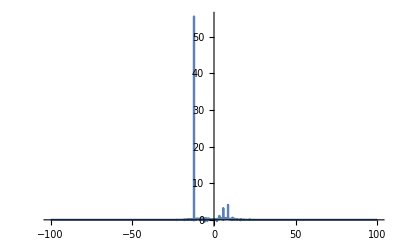

```mathematica
Plot[ϕ[0][p]H[0][p],{p,-100,100},PlotRange->All]
```

```mathematica
NIntegrate[ϕ[0][p]H[0][p],{p,-50,50},MaxRecursion->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in p near {p} = {-4.28486}. NIntegrate obtained 6.69847 and 0.0568444 for the integral and error estimates.

6.69847

```mathematica
NIntegrate[ϕ[0][p]H[0][p],{p,-10,10},MaxRecursion->100,Method->{"GlobalAdaptive","MaxErrorIncreases"->20000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in p near {p} = {-0.496423}. NIntegrate obtained 5.36864 and 0.674091 for the integral and error estimates.

5.36864

```mathematica
NIntegrate[ϕ[0][p]H[0][p],{p,-50,50},Method->"MonteCarlo"]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 5.7538 and 1.05692 for the integral and error estimates.

5.7538

```mathematica
ϕ[0][p]H[0][p]/.p->10
```

-4.42007×10^-24